# Tarea 2, Mat1620L

## Preguntas

### 1)

a)

```mathematica
h[x_,y_]:=20+3 Sin[x/5] Cos[y/4]+x^2/100+y^2/150
a=Plot3D[h[x,y],{x,-20,20},{y,-10,10},PlotStyle->RGBColor[1,0,0]];
Show[a]
```

-Graphics3D-

describa las principales características que observa en el terreno;
R: Podemos notar que presenta una profundidad considerable cerca del punto (-10,0) en x e y,.
identifique visualmente zonas de mayor y menor altura;
R:  Profundidad de la gráfica en (-10,0) en (x,y), empieza a subir a medida que y va hacia el infinito negativo y positivo, y una “colina” cercana al punto (10,0), actuando casi como un espejo de arriba a abajo con el primer punto mencionado.
explique por que el dominio escogido resulta adecuado para realizar este análisis.
R: Se ocupa (-20,20) en x para visualizar de mejor manera la profundidad a la que se va el terreno cerca del punto (10,0) donde también es posible visualizar las subidas cuando y tiende a infinito negativo y/o positivo.

b)

```mathematica
L[x_,y_]=h[2,1]+(x-2)*(D[h[x,y],x]/. {x->2,y->1})+(y-1)*(D[h[x,y],y]/. {x->2,y->1});
a=Plot3D[h[x,y],{x,-5,5},{y,-5,5},PlotStyle->RGBColor[1,0,0]];

b=Plot3D[L[x,y],{x,-3,3},{y,-3,3},PlotStyle->RGBColor[0,1,0]];

(*Visualización en dominio mayor*)
Show[{a,b}]
a=Plot3D[h[x,y],{x,-10,10},{y,-10,10},PlotStyle->RGBColor[1,0,0]];

b=Plot3D[L[x,y],{x,-5,5},{y,-5,5},PlotStyle->RGBColor[0,1,0]];

Show[{a,b}]
```

-Graphics3D-

-Graphics3D-

```mathematica
□_□
```

Explique que información del terreno conserva la aproximación L y que información no
puede reproducir.
R: A partir del plano verde que representa a L(x,y), podemos observar que conserva de manera casi idéntica la altura con respecto a h(x,y) y la inclinación a la que está la colina mencionada cerca del punto (x=2, y=1), sin embargo, esta aproximación no es del todo precisa puesto que no representa la curvatura y ondulaciones de dicha colina.

c)

```mathematica
L[x_,y_]=h[2.3,0.8]+(x-2)*(D[h[x,y],x]/. {x->2,y->1})+(y-1)*(D[h[x,y],y]/. {x->2,y->1});

a=Plot3D[h[x,y],{x,-10,10},{y,-10,10},PlotStyle->RGBColor[1,0,0]];
b=Plot3D[L[x,y],{x,-5,5},{y,-5,5},PlotStyle->RGBColor[0,1,0]];

Show[{a,b}]
(*Evaluación en el punto (2.3, 0.8)*)
L[2.3,0.8]
h[2.3,0.8]

Abs[L[2.3,0.8]-h[2.3,0.8]]
```

-Graphics3D-

21.5469

21.3625

0.184422

Compare esta estimación con el valor obtenido al evaluar directamente h(2,3, 0,8) y
calcule el error absoluto cometido.
R:  El cálculo del error absoluto resulta de 0.184, un error muy bajo y aceptable.
A partir del resultado obtenido, comente si considera razonable utilizar L para describir
el terreno entre los puntos P y Q.
R:Considero que sí es razonable ocupar el punto P y Q para describir el terreno puesto que son valores muy cercanos entre sí, además que su error absoluto es muy bajo.
d)

```mathematica
Q2[x_,y_] = h[2,1]+
(x-2)*(D[h[x,y],x]/. {x->2,y->1})+
(y-1)*(D[h[x,y],y]/. {x->2,y->1})+
((x-2)^2)/2*(D[D[h[x,y],x],x]/. {x->2,y->1})+
(x-2) (y-1) (D[D[h[x,y],x],y]/. {x->2,y->1})+
((y-1)^2)/2*(D[D[h[x,y],y],y]/. {x->2,y->1});

a=Plot3D[h[x,y],{x,-10,10},{y,-10,10},PlotStyle->RGBColor[1,0,0]];
b=Plot3D[L[x,y],{x,-5,5},{y,-5,5},PlotStyle->RGBColor[0,1,0]];
c = Plot3D[Q2[x,y],{x,-5,5},{y,-5,5},PlotStyle->RGBColor[0,0,1]];

Show[{a,b,c}]
Show[{a,c}]
Q2[2.3,0.8]
h[2.3,0.8]

Abs[Q[2.3,0.8]-h[2.3,0.8]]
```

-Graphics3D-

-Graphics3D-

21.3628

21.3625

Abs[-21.3625+Q[2.3,0.8]]

Compare las dos aproximaciones tanto numérica como gráficamente y explique las diferencias observadas.
R: Podemos observar que la gráfica de la función Q_2 se va asemejando mucho más al gráfico de h, la curvatura ya es más notoria con esta aproximación por el segundo polinomio de Taylor, además, el error absoluto ya es muchísimo menor, por lo cual conseguimos una aproximación más precisa con respecto a L(x,y).



Nota: En mi sesión de clases y labs no encontré la definición del segundo polinomio de Taylor, así que me basé en este enlace para deducirlo a código:

 https://foro.rinconmatematico.com/index.php?topic=73272.0 


e)

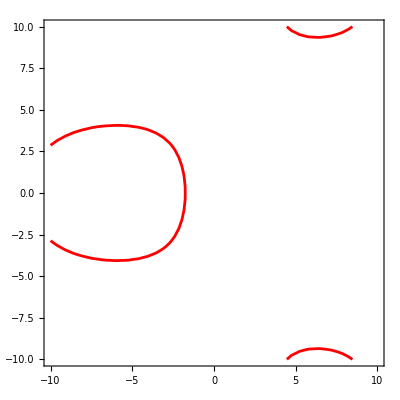

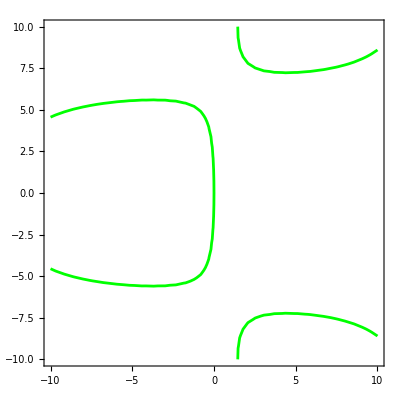

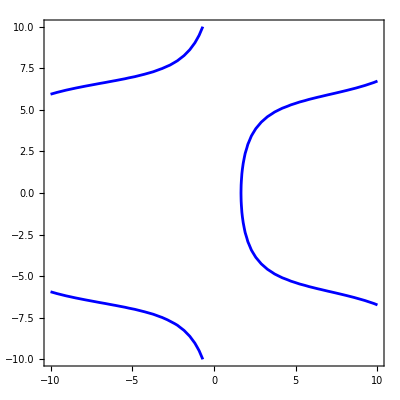

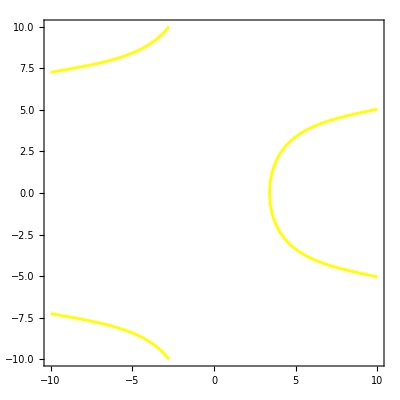

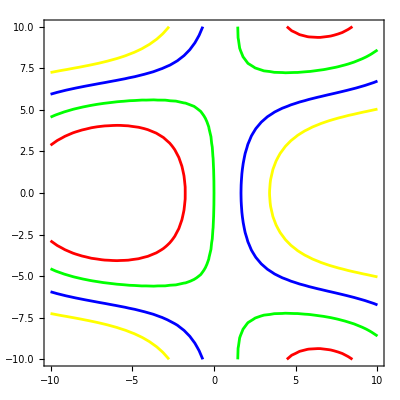

```mathematica
a1=ContourPlot[h[x,y]==19,{x,-10,10},{y,-10,10},ContourStyle->RGBColor[1,0,0]]
b1=ContourPlot[h[x,y]==20,{x,-10,10},{y,-10,10},ContourStyle->RGBColor[0,1,0]]
c1=ContourPlot[h[x,y]==21,{x,-10,10},{y,-10,10},ContourStyle->RGBColor[0,0,1]]
d1= ContourPlot[h[x,y]==22,{x,-10,10},{y,-10,10},ContourStyle->RGBColor[1,1,0]]
Show[{a1,b1,c1,d1}]
```

f)

```mathematica
Manipulate[ContourPlot[h[x,y]==H,{x,-10,10},{y,-10,10},PlotLabel->"H="<>ToString[H],ContourStyle->RGBColor[0,0,1]], {H,18,25,0.5}]
a=Plot3D[h[x,y],{x,-10,10},{y,-10,10},PlotStyle->RGBColor[1,0,0]];

p1 = Plot3D[z= 19,{x,-10,10},{y,-10,10},PlotStyle->RGBColor[0,0,1]];
p2 = Plot3D[z= 20,{x,-10,10},{y,-10,10},PlotStyle->RGBColor[0,0,1]];
p3 = Plot3D[z= 21,{x,-10,10},{y,-10,10},PlotStyle->RGBColor[0,0,1]];
p4 = Plot3D[z= 22,{x,-10,10},{y,-10,10},PlotStyle->RGBColor[0,0,1]];

Show[{a,p1}]
Show[{a,p2}]
Show[{a,p3}]
Show[{a,p4}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

A partir de la animación, identifique algún valor o intervalo de valores de .b4 H para el cual
se produzca un cambio cualitativo importante en la región inundada. Explique claramente
en qué consiste dicho cambio.
R: En conjunto de los gráficos 3D de apoyo para poder visualizar la subida del agua en este terreno y las curvas de nivel de la primera gráfica podemos notar que a partir de H = 20 y H=21,  la mayor parte del terreno comienza a quedar debajo del nivel del agua


g) Sin respuesta

```mathematica
(*Sin respuesta*)
```

h)

```mathematica
h[x_,y_]:=20+3 Sin[x/5] Cos[y/4]+x^2/100+y^2/150;
Q2[x_,y_] = h[2,1]+
(x-2)*(D[h[x,y],x]/. {x->2,y->1})+
(y-1)*(D[h[x,y],y]/. {x->2,y->1})+
((x-2)^2)/2*(D[D[h[x,y],x],x]/. {x->2,y->1})+
(x-2) (y-1) (D[D[h[x,y],x],y]/. {x->2,y->1})+
((y-1)^2)/2*(D[D[h[x,y],y],y]/. {x->2,y->1});

p1 = Plot3D[z= 19,{x,-10,10},{y,-10,10},PlotStyle->RGBColor[0,0,1]];
p2 = Plot3D[z= 20,{x,-10,10},{y,-10,10},PlotStyle->RGBColor[0,0,1]];
p3 = Plot3D[z= 21,{x,-10,10},{y,-10,10},PlotStyle->RGBColor[0,0,1]];
p4 = Plot3D[z= 22,{x,-10,10},{y,-10,10},PlotStyle->RGBColor[0,0,1]];



a=Plot3D[h[x,y],{x,-3,3},{y,-3,3},PlotStyle->RGBColor[1,0,0]];
b=Plot3D[Q2[x,y],{x,-3,3},{y,-3,3},PlotStyle->RGBColor[1,1,0]];
Show[{a,b,p3}]


a=Plot3D[h[x,y],{x,-10,10},{y,-10,10},PlotStyle->RGBColor[1,0,0]];
b=Plot3D[Q2[x,y],{x,-10,10},{y,-10,10},PlotStyle->RGBColor[1,1,0]];
Show[{a,b,p3}]


a=Plot3D[h[x,y],{x,-25,25},{y,-25,25},PlotStyle->RGBColor[1,0,0]];
b=Plot3D[Q2[x,y],{x,-25,25},{y,-25,25},PlotStyle->RGBColor[1,1,0]];
Show[{a,b,p3}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

A partir de sus resultados, explique en que circunstancias considera razonable utilizar
la aproximación cuadrática para estudiar la inundación y en que circunstancias dicha
aproximación puede conducir a conclusiones incorrectas.

Su conclusión debe relacionar explícitamente lo observado con el hecho de que Q2 es
una aproximación local de la función h alrededor del punto P.

R:  Podemos observar en la primera gráfica que al acercarnos más al punto al cual hicimos la segunda aproximación lineal la gráfica 3d se asemeja a la gráfica original h(x,y), sin embargo, a medida que nos alejamos en el dominio x e y, notaremos que va perdiendo precisión puesto que solo fue una aproximación local al punto (2,1), valores más lejanos no tendrán sentido para la Linealización y ocuparlo para evaluar el terreno con respecto a la subida del agua no nos será muy efectivo, a menos que, evaluemos cerca de ese punto.